## Initialization

```mathematica
Get["G:\\My Drive\\PhD Pisa\\Calculations, Data and Designs\\Wolfram Mathematica\\SuperPackage.m"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

G:\My Drive\PhD Pisa\Calculations, Data and Designs\Wolfram Mathematica\TSQUIPT thermal transport

```mathematica
SetΔ0[200 1.6 10^-25];
Setγ[10^-4];
SetvF[2.3 10^6];

Tc = GetΔ0[]/(1.764*kB); (*Real value of the BCS critical temperature*)
ξ0=(* 1/Δ0 *) ℏ*GetvF[]; (* ξ0 is rescaled by Δ0, which causes the Δ0 to drop out. This rescaled ξ0 is thus in units of m×Δ0 *)
```

```mathematica
{GetΔ0[],GetTc[],Getγ[],GetvF[]}
```

{3.2×10^-23,1.31401[],1/10000,2.3×10^6}

## General plots

### Global parameters defined in SuperPackage

```mathematica
{kB,q,Φ0,h,ℏ}
```

{1.38065×10^-23,1.60218×10^-19,2.067×10^-15,6.62607×10^-34,1.05457×10^-34}

### Superconducting gap

```mathematica
?Δ
```

Δ[T] 
 Gives the gap.

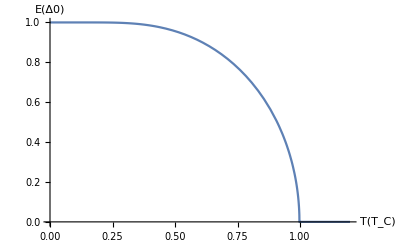

```mathematica
Plot[Δ[x],{x,0,1.2},AxesLabel->{"T(T_C)","E(Δ0)"}]
```

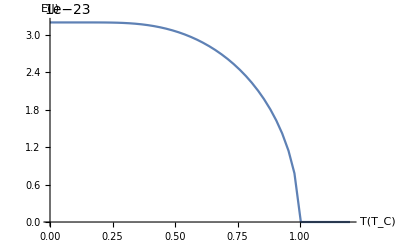

```mathematica
Plot[Δ[x,rescale -> False],{x,0,1.2},AxesLabel->{"T(T_C)","E(J)"}]
```

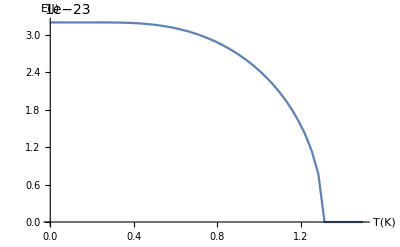

```mathematica
Plot[Δ[(x/Tc) ,rescale -> False],{x,0,1.5},AxesLabel->{"T(K)","E(J)"}]
```

### Fermi function

```mathematica
Information["fermi",LongForm->False]
```

fermi[energy,T] 
 The Fermi districution function.

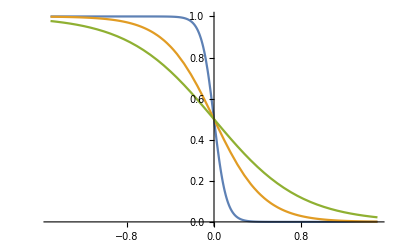

```mathematica
Plot[{fermi[x,0.1],fermi[x,0.4],fermi[x,0.7]},{x,-1.5,1.5}]
```

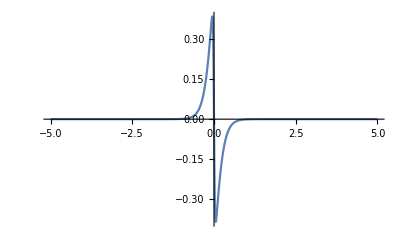

```mathematica
Plot[fermi[energy,0.025]-fermi[energy,0.25],{energy,-5,5},PlotRange->Full]
```

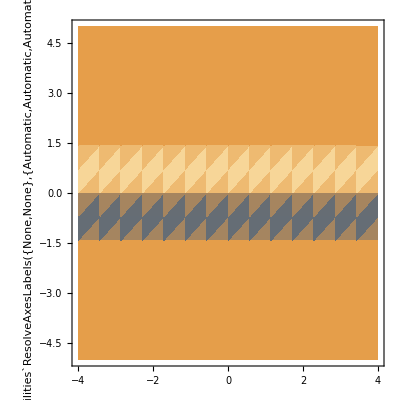

```mathematica
DensityPlot[fermi[energy,0.25]-fermi[energy,0.025],{x,-4,4},{energy,-5,5},PlotRange->Full]
```

With a voltage bias

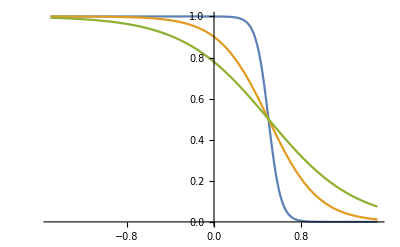

```mathematica
Module[{V=0.5},Plot[{fermi[energy-V,0.1],fermi[energy-V,0.4],fermi[energy-V,0.7]},{energy,-1.5,1.5}]]
```

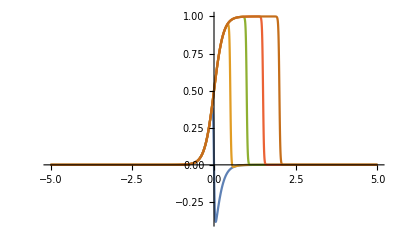
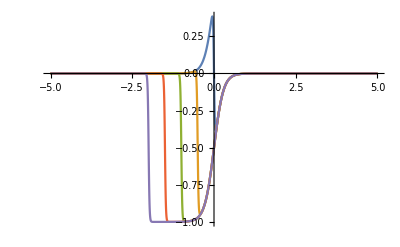
{Legended[-Graphics-,Placed[LineLegend[{Directive[Opacity[1.],RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]],Directive[Opacity[1.],RGBColor[0.880722, 0.611041, 0.142051],AbsoluteThickness[1.6]],Directive[Opacity[1.],RGBColor[0.560181, 0.691569, 0.194885],AbsoluteThickness[1.6]],Directive[Opacity[1.],RGBColor[0.922526, 0.385626, 0.209179],AbsoluteThickness[1.6]],Directive[Opacity[1.],RGBColor[0.528488, 0.470624, 0.701351],AbsoluteThickness[1.6]],Directive[Opacity[1.],RGBColor[0.772079, 0.431554, 0.102387],AbsoluteThickness[1.6]]},{V = 0 Δ0/q,V = 0.5 Δ0/q,V = 1 Δ0/q,V = 1.5 Δ0/q,V = 2 Δ0/q},LegendMarkers→None,LabelStyle→{},LegendLayout→Column],After]],Legended[-Graphics-,Placed[LineLegend[{Directive[Opacity[1.],RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]],Directive[Opacity[1.],RGBColor[0.880722, 0.611041, 0.142051],AbsoluteThickness[1.6]],Directive[Opacity[1.],RGBColor[0.560181, 0.691569, 0.194885],AbsoluteThickness[1.6]],Directive[Opacity[1.],RGBColor[0.922526, 0.385626, 0.209179],AbsoluteThickness[1.6]],Directive[Opacity[1.],RGBColor[0.528488, 0.470624, 0.701351],AbsoluteThickness[1.6]]},{V = -0 Δ0/q,V = -0.5 Δ0/q,V = -1 Δ0/q,V = -1.5 Δ0/q,V = -2 Δ0/q},LegendMarkers→None,LabelStyle→{},LegendLayout→Column],After]]}

```mathematica
{Plot[{fermi[energy+0,0.025]-fermi[energy,0.25],fermi[energy-0.5,0.025]-fermi[energy,0.25],fermi[energy-1,0.025]-fermi[energy,0.25],fermi[energy-1.5,0.025]-fermi[energy,0.25],Null,fermi[energy-2,0.025]-fermi[energy,0.25]},{energy,-5,5},PlotRange->Full,PlotLegends->{"V = 0 \!\(\*FractionBox[\(Δ0\), \(q\)]\)","V = 0.5 \!\(\*FractionBox[\(Δ0\), \(q\)]\)","V = 1 \!\(\*FractionBox[\(Δ0\), \(q\)]\)","V = 1.5 \!\(\*FractionBox[\(Δ0\), \(q\)]\)","V = 2 \!\(\*FractionBox[\(Δ0\), \(q\)]\)"}],Plot[{fermi[energy+0,0.025]-fermi[energy,0.25],fermi[energy+0.5,0.025]-fermi[energy,0.25],fermi[energy+1,0.025]-fermi[energy,0.25],fermi[energy+1.5,0.025]-fermi[energy,0.25],fermi[energy+2,0.025]-fermi[energy,0.25]},{energy,-5,5},PlotRange->Full,PlotLegends->{"V = -0 \!\(\*FractionBox[\(Δ0\), \(q\)]\)","V = -0.5 \!\(\*FractionBox[\(Δ0\), \(q\)]\)","V = -1 \!\(\*FractionBox[\(Δ0\), \(q\)]\)","V = -1.5 \!\(\*FractionBox[\(Δ0\), \(q\)]\)","V = -2 \!\(\*FractionBox[\(Δ0\), \(q\)]\)"}]}
```

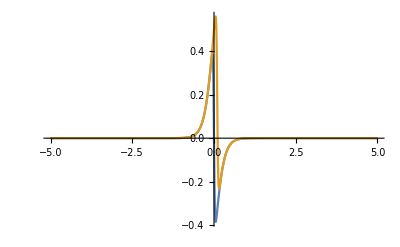
Legended[-Graphics-,Placed[LineLegend[{Directive[Opacity[1.],RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]],Directive[Opacity[1.],RGBColor[0.880722, 0.611041, 0.142051],AbsoluteThickness[1.6]]},{V = 0 Δ0/q,V = 0.1 Δ0/q},LegendMarkers→None,LabelStyle→{},LegendLayout→Column],After]]

```mathematica
Plot[{fermi[energy+0,0.025]-fermi[energy,0.25],fermi[energy-0.1,0.025]-fermi[energy,0.25]},{energy,-5,5},PlotRange->Full,PlotLegends->{"V = 0 \!\(\*FractionBox[\(Δ0\), \(q\)]\)","V = 0.1 \!\(\*FractionBox[\(Δ0\), \(q\)]\)"}]
```

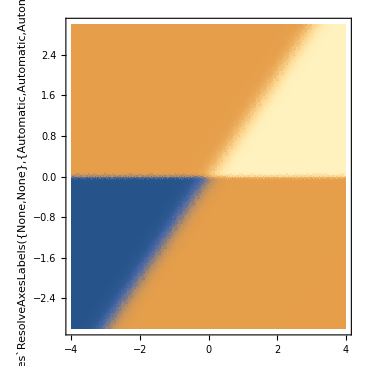
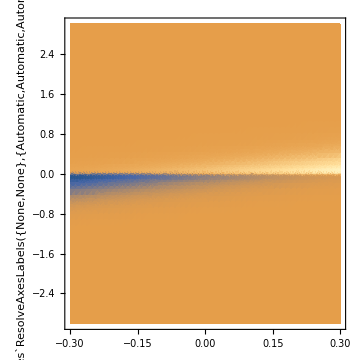

```mathematica
{DensityPlot[fermi[energy-V,0.25]-fermi[energy,0.025],{V,-4,4},{energy,-3,3},PlotRange->Full,PlotPoints->50],DensityPlot[fermi[energy-V,0.25]-fermi[energy,0.025],{V,-0.3,0.3},{energy,-3,3},PlotRange->Full,PlotPoints->50]}
```

### Quasiparticle density of states

```mathematica
?ρQP
```

ρQP[energy,T] 
 The BCS quasiparticle density of states.

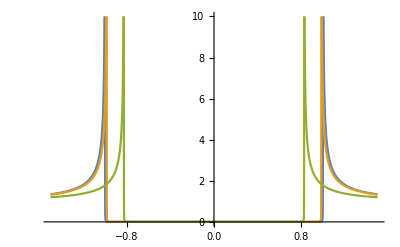

```mathematica
Plot[{ρQP[x,0.1],ρQP[x,0.4],ρQP[x,0.7]},{x,-1.5,1.5},PlotRange->{0,10}]
```

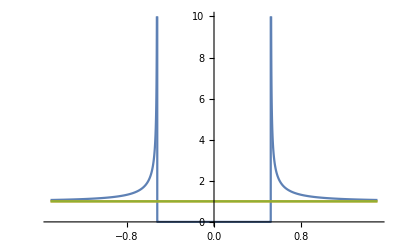

```mathematica
Plot[{ρQP[x,0.9],ρQP[x,1.2],ρQP[x,1.5]},{x,-1.5,1.5},PlotRange->{0,10}]
```

### Transmission of a topological Josephson junction

```mathematica
?transmissionTJJ
```

transmissionTJJ[energy, flux, T, L, ϕ0:0] 
 The transmission function of a topological Josepson junction not including the Andreev bound states. The length is expected in units of ξ0 (which is itself rescaled by Δ0). The superconducting phase difference ϕ0 is optional, and 0 by default.

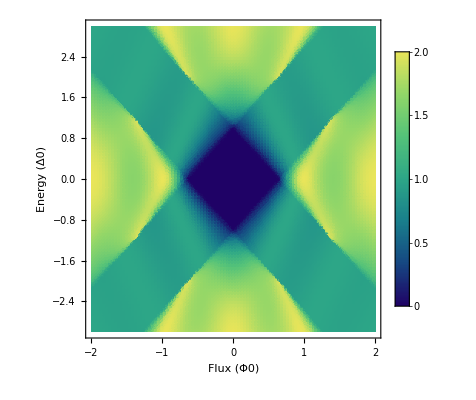

```mathematica
DensityPlot[transmissionTJJ[energy,flux,0.1,1 ξ0],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)","Transmission"}]
```

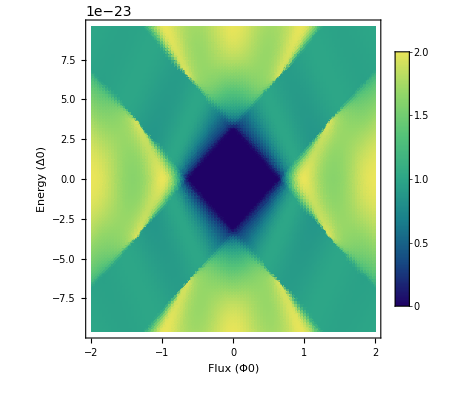

```mathematica
Module[{Δ0 = 200*1.6 10^-25},DensityPlot[transmissionTJJ[energy/Δ0,flux,0.1,1 ξ0],{flux,-2,2},{energy,-3Δ0,3Δ0},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)","Transmission"}]]
```

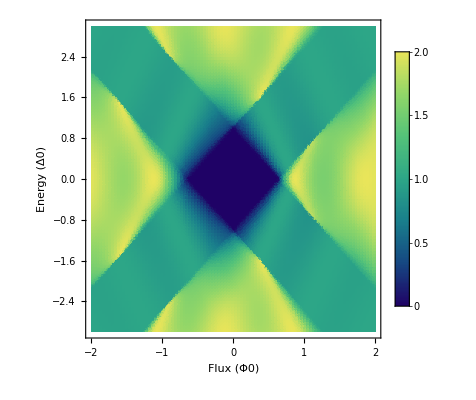

```mathematica
DensityPlot[transmissionTJJ[energy,flux,0.1,1 ξ0,0.25 Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)","Transmission"}]
```

#### Individial edges

```mathematica
?transmissionTJJU
```

transmissionTJJ[energy, flux, T, L, ϕ0:0] 
 The transmission function of a topological Josepson junction for right-moving particles along the upper edge, not including the Andreev bound states. The length is expected in units of ξ0 (which is itself rescaled by Δ0). The superconducting phase difference ϕ0 is optional, and 0 by default.

```mathematica
DensityPlot[transmissionTJJU[energy,flux,0.1,1 ξ0,0.25 Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)","Transmission"}]
```

-Graphics-

```mathematica
?transmissionTJJL
```

transmissionTJJ[energy, flux, T, L, ϕ0:0] 
 The transmission function of a topological Josepson junction for right-moving particles along the lower edge, not including the Andreev bound states. The length is expected in units of ξ0 (which is itself rescaled by Δ0). The superconducting phase difference ϕ0 is optional, and 0 by default.

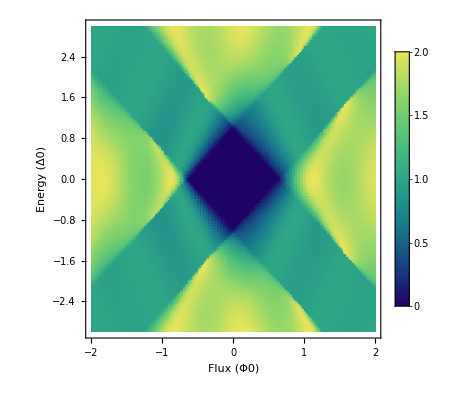

```mathematica
DensityPlot[transmissionTJJL[energy,flux,0.1,1 ξ0,0.25 Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)","Transmission"}]
```

### Topological Josephson junction density of states, without ABS

```mathematica
?ρTJJ
```

ρTJJ[energy, flux, T, L, ϕ0:0] 
 The density of states of a topological Josephson junction, not including the Andreev bound states. The length is expected in units of ξ0 (which is itself rescaled by Δ0). The superconducting phase difference ϕ0 is optional, and 0 by default.

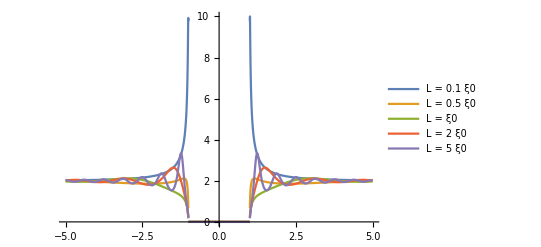

```mathematica
Plot[{ρTJJ[energy,0,0.1,0.1ξ0],ρTJJ[energy,0,0.1,0.5ξ0],ρTJJ[energy,0,0.1,ξ0],ρTJJ[energy,0,0.1,2ξ0],ρTJJ[energy,0,0.1,5ξ0]},{energy,-5,5},PlotRange->Full,PlotLegends->{"L = 0.1 ξ0","L = 0.5 ξ0","L =  ξ0","L = 2 ξ0","L = 5 ξ0"}]
```

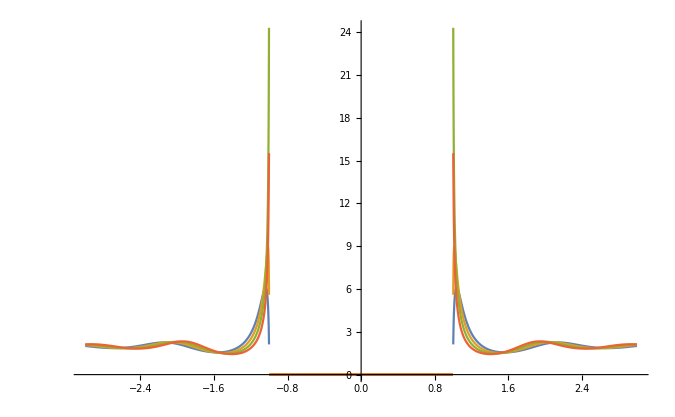

```mathematica
Plot[{ρTJJ[energy,0,0.1,2.9 ξ0],ρTJJ[energy,0,0.1,3 ξ0],ρTJJ[energy,0,0.1,3.1 ξ0],ρTJJ[energy,0,0.1,3.2 ξ0]},{energy,-3,3},PlotRange->Full]
```

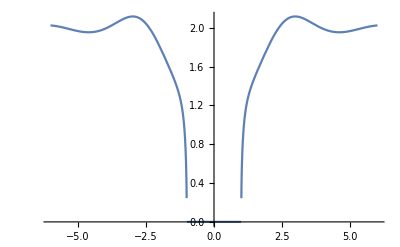
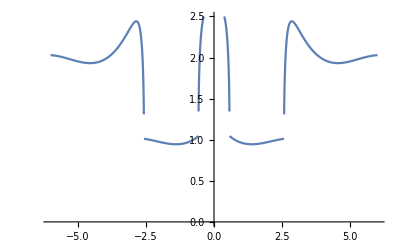
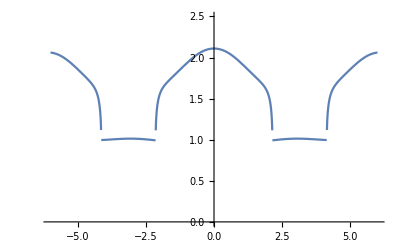
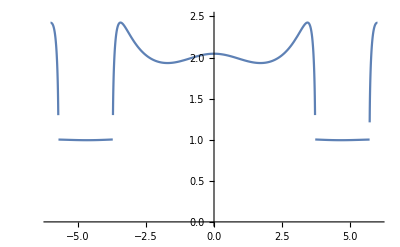
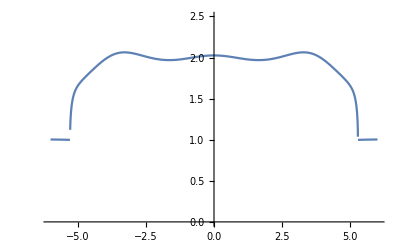

```mathematica
{Plot[ρTJJ[energy,0,0.1, ξ0],{energy,-6,6},PlotRange->Full,PlotRange->{0,2.5}],Plot[ρTJJ[energy,1,0.1, ξ0],{energy,-6,6},PlotRange->{0,2.5}],Plot[ρTJJ[energy,2,0.1, ξ0],{energy,-6,6},PlotRange->{0,2.5}],Plot[ρTJJ[energy,3,0.1, ξ0],{energy,-6,6},PlotRange->{0,2.5}],Plot[ρTJJ[energy,4,0.1, ξ0],{energy,-6,6},PlotRange->{0,2.5}]}
```

#### Comparison with NIS junction

```mathematica
?ρQP
```

ρQP[energy,T] 
 The BCS quasiparticle density of states.

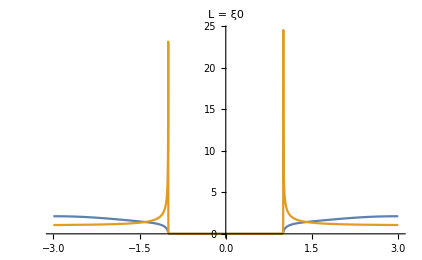
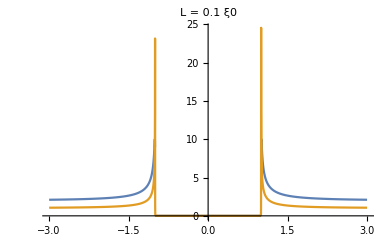
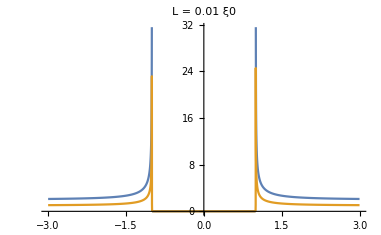
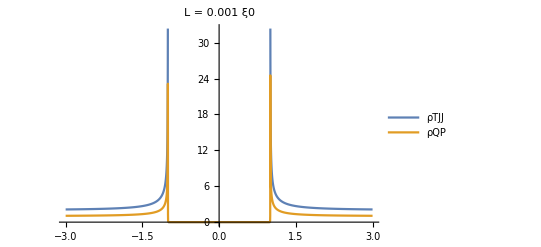

```mathematica
{Plot[{ρTJJ[energy,0,0.1,1ξ0],ρQP[energy,0.1]},{energy,-3,3},PlotRange->Full,PlotLabel->"L = ξ0"],Plot[{ρTJJ[energy,0,0.1,0.1ξ0],ρQP[energy,0.1]},{energy,-3,3},PlotRange->Full,PlotLabel->"L = 0.1 ξ0"],Plot[{ρTJJ[energy,0,0.1,0.01ξ0],ρQP[energy,0.1]},{energy,-3,3},PlotRange->Full,PlotLabel->"L = 0.01 ξ0"],Plot[{ρTJJ[energy,0,0.1,0.001ξ0],ρQP[energy,0.1]},{energy,-3,3},PlotRange->Full,PlotLabel->"L = 0.001 ξ0",PlotLegends->{"ρTJJ","ρQP"}]}
```

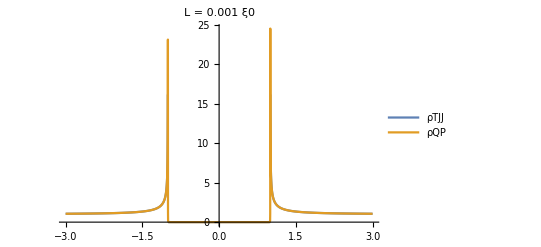

```mathematica
Plot[{ρTJJ[energy,0,0.1,0.001ξ0]/2,ρQP[energy,0.1]},{energy,-3,3},PlotRange->Full,PlotLabel->"L = 0.001 ξ0",PlotLegends->{"ρTJJ","ρQP"}]
```

#### Density plots

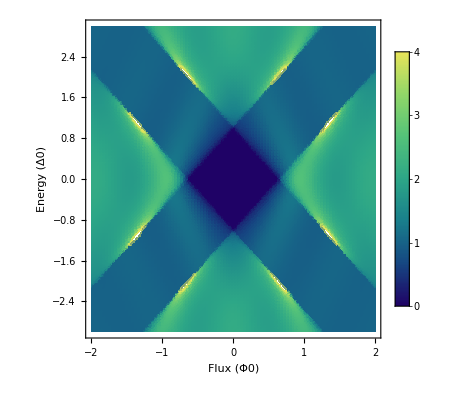

```mathematica
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}]
```

#### ϕ0 dependency

```mathematica
{DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,0Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,0.25Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,0.5Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,.75Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,1.25Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,1.5Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,1.75Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Topological Josephson junction density of states, without ABS, with an assymmetric bias

One of the two superconductors has a chemical potential μ > 0 , while that of the probe and the other superconducting lead is zero.

```mathematica
transmissionTJJUR[energy_,flux_,T_,L_,ϕ0_:0]:= HeavisideTheta[Abs[energyMin[energy,flux,L]
]-Δ[T]]*((energyMin[energy,flux,L]^2-Δ[T]^2)/(energyMin[energy,flux,L]^2-Δ[T]^2 Cos[(ϕ0+Pi*flux)/2-(energyMin[energy,flux,L]*L)/(ℏ vF)]^2))+ HeavisideTheta[Abs[energyPlus[energy,flux,L]
]-Δ[T]]*((energyPlus[energy,flux,L]^2-Δ[T]^2)/(energyPlus[energy,flux,L]^2-Δ[T]^2 Cos[(ϕ0+Pi*flux)/2+(energyPlus[energy,flux,L]*L)/(ℏ vF)]^2));
```

## Thermal transport Normal probe

### JNIS

```mathematica
?JNIS
```

JNIS[tempN, tempS, γ:0, RTunnelProbe:1, rescale -> True] 
 The heat current through an NIS tunnel junction.

```mathematica
JNIS[0.025,0.9]
```

-0.455414

```mathematica
{Plot[JNIS[0.025,TempS],{TempS,0.025,2}],Plot[JNIS[TempN,0.025],{TempN,0.025,2}]}
```

{-Graphics-,-Graphics-}

```mathematica
{DensityPlot[JNIS[TNormal,TSuper],{TNormal,0.025,2},{TSuper,0.025,2},FrameLabel->{"TNormal (T_C)","TSuper (T_C)"},PlotLegends->Automatic],Plot3D[JNIS[TNormal,TSuper],{TNormal,0.025,2},{TSuper,0.025,2},AxesLabel->{"TNormal (T_C)","TSuper (T_C)"},PlotLegends->Automatic]}
```

{-Graphics-,-Graphics3D-}

#### Rectification coefficients JNIS

Replication of the NIS plot in Fig. 1 of the “Efficient phase-tunable Josephson thermal rectifier” paper, doi: 10.1063/1.4804550

```mathematica
$MachinePrecision
```

15.9546

```mathematica
ρQP[Δ[0.1],0.1]
```

Power::infy: Infinite expression 1/0. encountered.

Indeterminate

```mathematica
Plot[rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.01,Thot],{Thot,0.01,2},AxesLabel->{"THot (T_C)","R (%)"},PlotLegends->{"TCold = 0.01 T_C","TCold = 0.3 T_C","TCold = 0.4 T_C","TCold = 0.5 T_C","TCold = 0.6 T_C","TCold = 0.7 T_C"}]
```

-Graphics-

```mathematica
Plot[{rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.01,Thot],
rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.3,Thot],
rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.4,Thot],
rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.5,Thot],
rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.6,Thot],
rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.7,Thot]},{Thot,0.01,2},AxesLabel->{"THot (T_C)","R (%)"},PlotLegends->{"TCold = 0.01 T_C","TCold = 0.3 T_C","TCold = 0.4 T_C","TCold = 0.5 T_C","TCold = 0.6 T_C","TCold = 0.7 T_C"}]
```

-Graphics-

```mathematica
Module[{gamma = 10^-5},Plot[{rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.01,Thot],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.3,Thot],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.5,Thot],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.7,Thot],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.9,Thot],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,1.1,Thot]},{Thot,0.01,2},AxesLabel->{"THot (T_C)","R (%)"},PlotLegends->{"TCold = 0.01 T_C","TCold = 0.3 T_C","TCold = 0.5 T_C","TCold = 0.7 T_C","TCold = 0.9 T_C","TCold = 1.1 T_C"}]]
```

-Graphics-

Inverse definition (T1 and T2 reversed)

```mathematica
Module[{gamma = 10^-5},Plot[{rectCoefficientRelative[JNIS[T1,T2],T1,T2,Thot,0.01],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,Thot,0.3],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,Thot,0.4],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,Thot,0.5],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,Thot,0.6],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,Thot,0.7]},{Thot,0.01,2},AxesLabel->{"THot (T_C)","R (%)"},PlotLegends->{"TCold = 0.01 T_C","TCold = 0.3 T_C","TCold = 0.4 T_C","TCold = 0.5 T_C","TCold = 0.6 T_C","TCold = 0.7 T_C"}]]
```

-Graphics-

### Thermal conductance TJJ

```mathematica
?thermalConductanceTJJ
```

thermalConductanceTJJ[flux_,T_,L_,ϕ0:0,rescale -> True (False)] 
 The thermal conductance of a topological Josephson junction, in the linear approximation. When setting rescale -> False, a value for ϕ0 must be provided.

```mathematica
{thermalConductanceTJJ[1,0.1,1 ξ0],
thermalConductanceTJJ[1,0.1,1 ξ0, 0],
thermalConductanceTJJ[1,0.1,1 ξ0, 0,rescale -> True],
thermalConductanceTJJ[1,0.1,1 ξ0,0,rescale -> False]}
```

{0.202978,0.202978,0.202978,2.38723×10^-13}

```mathematica
?GQ
```

GQ[T] 
 The quantum of thermal conductance. Input T is expected in units of Tc, as per usual.

```mathematica
GQ[0.1]
```

9.46433×10^-14

```mathematica
Plot[{thermalConductanceTJJ[flux,0.1,ξ0,0,rescale->False]/GQ[0.1 ],thermalConductanceTJJ[flux,0.2,ξ0,0,rescale->False]/GQ[0.2 ],thermalConductanceTJJ[flux,0.4,ξ0,0,rescale->False]/GQ[0.4 ]},{flux,-5,5 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K"},PlotLabel->"Thermal conductance for L = ξ0 and ϕ0 = 0, in units of the thermal conductance quantum"]
```

-Graphics-

```mathematica
Plot[{thermalConductanceTJJ[flux,0.1,ξ0],thermalConductanceTJJ[flux,0.2,ξ0],thermalConductanceTJJ[flux,0.4,ξ0]},{flux,-5 ,5 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K"},PlotLabel->"Thermal conductance for L = ξ0 and ϕ0 = 0"]
```

-Graphics-

```mathematica
Plot[{thermalConductanceTJJ[flux,0.1,3ξ0]/GQ[0.1],thermalConductanceTJJ[flux,0.2,3ξ0]/GQ[0.2],thermalConductanceTJJ[flux,0.4,3ξ0]/GQ[0.4],thermalConductanceTJJ[flux,0.6,3ξ0]/GQ[0.6],thermalConductanceTJJ[flux,0.8,3ξ0]/GQ[0.8]},{flux,-10 ,10 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K","T = 0.6 K","T = 0.8 K"},PlotLabel->"Thermal conductance for L = 3ξ0 and ϕ0 = 0, in units of the thermal conductance quantum",PlotRange->Automatic]
```

-Graphics-

```mathematica
Plot3D[thermalConductanceTJJ[flux,0.1,1 ξ0](ΔT),{ΔT,0,1},{flux,0,2.5},AxesLabel->{"ΔT","Flux","JJunction"}, PlotLegends -> {"T TI = 0.1 Tc"}]
```

-Graphics3D-

#### thermalConductanceTJJ rescaling check

```mathematica
Module[{T=0.1,L=ξ0,ϕ0=0,Δ0 = 200 1.6 10^-25},
Plot[{thermalConductanceTJJ[flux,0.1,1 ξ0,0,rescale -> False],1/h NIntegrate[(energy^2 transmissionTJJ[energy/Δ0,flux,T,L,ϕ0])/(4kB T^2 Tc^2 Cosh[energy/(2 kB T Tc)]^2),{energy,-10Δ0,10Δ0},MaxRecursion->25,MinRecursion->5,AccuracyGoal->10,Method->Oscillatory]},{flux,0,3}]]
-Graphics-
```

```mathematica
Module[{flux=0.34,L=ξ0,ϕ0=0,Δ0 = 200 1.6 10^-25},
Plot[{thermalConductanceTJJ[flux,T,1 ξ0,0,rescale -> False],1/h NIntegrate[(energy^2 transmissionTJJ[energy/Δ0,flux,T ,L,ϕ0])/(4kB T^2 Tc^2 Cosh[energy/(2 kB T Tc)]^2),{energy,-10Δ0,10Δ0},MaxRecursion->25,MinRecursion->5,AccuracyGoal->10,Method->Oscillatory]},{T,0.1,.8}]]
```

-Graphics-

### Nonlinear heat current through a TJJ

```mathematica
?JJunctionNonLinear
```

JJunctionNonLinear [flux, Ts1, Ts2, L, ϕ0:0, rescale -> True (False)] 
 The (non linear) heat current through a topological Josephson junction.

```mathematica
Module[{Ts1=0.5,Ts2 = 0.025,L=ξ0},
Plot[{JJunctionLinear[flux,Ts1,Ts2,L],JJunctionNonLinear[flux,Ts1,Ts2,L]},{flux,-4,4}]]
```

-Graphics-

```mathematica
Module[{Ts2 = 0.025,L=ξ0,plotOptions = {ImageSize -> Medium,AxesLabel->{"Flux (Φ0)","J (Δ_0^2/h)"},PlotLegends-> {"J linear","J nonlinear"}}},
{Plot[{JJunctionLinear[flux,0.1,Ts2,L],JJunctionNonLinear[flux,0.1,Ts2,L]},{flux,-4,4},Evaluate[plotOptions]],
Plot[{JJunctionLinear[flux,0.5,Ts2,L],JJunctionNonLinear[flux,0.5,Ts2,L]},{flux,-4,4},Evaluate[plotOptions]],
Plot[{JJunctionLinear[flux,0.9,Ts2,L],JJunctionNonLinear[flux,0.9,Ts2,L]},{flux,-4,4},Evaluate[plotOptions]]}]
```

{-Graphics-,-Graphics-,-Graphics-}

### GNProbe

```mathematica
?GNProbe
```

GNProbeLinear[flux, T, L, ϕ0:0, V:0 ,RTunnelProbe:1, rescale -> True] 
 The thermal conductance of a normal probe - TJJ.

```mathematica
GNProbe[0, 0.1, ξ0]
```

3.60585×10^-7

```mathematica
GNProbe[0, 0.1, ξ0,0,0,1,rescale -> False]
```

1.09469×10^-14

```mathematica
Plot[GNProbe[0, T, ξ0],{T,0.1,2}]
```

-Graphics-

```mathematica
Plot[GNProbe[0, 0.1, L ξ0],{L,0.1,5}]
```

-Graphics-

```mathematica
Plot[GNProbe[flux, 0.1, ξ0],{flux,-4,4}]
```

-Graphics-

```mathematica
{Plot[{thermalConductanceTJJ[flux,0.1,ξ0],thermalConductanceTJJ[flux,0.2,ξ0],thermalConductanceTJJ[flux,0.4,ξ0],thermalConductanceTJJ[flux,0.6,ξ0],thermalConductanceTJJ[flux,0.8,ξ0],thermalConductanceTJJ[flux,1,ξ0]},{flux,-5,5 },PlotLegends -> {"T = 0.1 Tc","T = 0.2 Tc","T = 0.4 Tc","T = 0.6 Tc","T = 0.8 Tc","T = 1 Tc"},PlotLabel->"Thermal conductance (Expression Björn) for L = ξ0 and ϕ0 = 0, in rescaled units"],
Plot[{GNProbe[flux,0.1,ξ0],GNProbe[flux,0.2,ξ0 ],GNProbe[flux,0.4,ξ0 ],GNProbe[flux,0.6,ξ0 ],GNProbe[flux,0.8,ξ0 ],GNProbe[flux,1,ξ0 ]},{flux,-5,5 },PlotLegends -> {"T = 0.1 Tc","T = 0.2 Tc","T = 0.4 Tc","T = 0.6 Tc","T = 0.8 Tc","T = 1 Tc"},PlotLabel->"Thermal conductance (GNProbe) for L = ξ0 and ϕ0 = 0, in units of the thermal conductance quantum / R_T"]}
```

{-Graphics-,-Graphics-}

```mathematica
{Plot[{thermalConductanceTJJ[flux,0.1,ξ0,0,rescale->False]/GQ[0.1 ],thermalConductanceTJJ[flux,0.2,ξ0,0,rescale->False]/GQ[0.2 ],thermalConductanceTJJ[flux,0.4,ξ0,0,rescale->False]/GQ[0.4 ]},{flux,-5,5 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K"},PlotLabel->"Thermal conductance (Expression Björn) for L = ξ0 and ϕ0 = 0, in units of the thermal conductance quantum"],
Plot[{GNProbe[flux,0.1,ξ0,0,0,25812.81079353287,rescale->False]/GQ[0.1 ],GNProbe[flux,0.2,ξ0,0,0,25812.81079353287,rescale->False]/GQ[0.2 ],GNProbe[flux,0.4,ξ0,0,0,25812.81079353287,rescale->False]/GQ[0.4 ]},{flux,-5,5 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K"},PlotLabel->"Thermal conductance (GNProbe) for L = ξ0 and ϕ0 = 0, in units of the thermal conductance quantum / R_T"]}
```

{-Graphics-,-Graphics-}

```mathematica
{Plot[{GNProbe[flux,0.1,ξ0]/GNProbe[4,0.1,ξ0],GNProbe[flux,0.2,ξ0]/GNProbe[4,0.2,ξ0],GNProbe[flux,0.4,ξ0]/GNProbe[4,0.4,ξ0]},{flux,-4,4 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K"},PlotLabel->"Thermal conductance (GNProbe) for L = ξ0 and ϕ0 = 0, in units of GNProbe[4,T,ξ0]"],
Plot[{GNProbe[flux,0.1,ξ0]/GNProbe[4,1,ξ0],GNProbe[flux,0.2,ξ0]/GNProbe[4,1,ξ0],GNProbe[flux,0.4,ξ0]/GNProbe[4,1,ξ0]},{flux,-4,4 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K"},PlotLabel->"Thermal conductance (GNProbe) for L = ξ0 and ϕ0 = 0, in units of GNProbe[4,T_C,ξ0]"]}
```

{-Graphics-,-Graphics-}

### JNProbe: heat current between a N probe and a TJJ

```mathematica
?JNProbe
```

JNProbe[flux, tempNProbe, tempJunction, L, ϕ0:0, RTunnelProbe:1, rescale -> True (False)] 
 The heat current between a normal metal probe, tunnel coupled to one side of a topological Josephson junction. The length is expected in units of ξ0 (which is itself rescaled by Δ0). Can be descaled using rescale -> False as the last argument, in this case ϕ0 and RTunnelProbe must be provided.

```mathematica
{JNProbe[0,0.5,0.1,1 ξ0],JNProbe[0,0.5,0.1,1 ξ0,0,0,10000],JNProbe[0,0.5,0.1,1 ξ0,0,0,10000,rescale->True],JNProbe[0,0.5,0.1,1 ξ0,0,0,10000,rescale->False]}
```

{0.0261171,0.0261171,0.0261171,1.04185×10^-13}

#### JNProbe integrand

Low temperatures

```mathematica
Module[{tempJunction = 0.025,tempNProbe = 0.25,L=ξ0,ϕ0=0,plotOptions ={Exclusions->None,PlotPoints->50,ImageSize -> Medium ,PlotLegends ->Automatic, FrameLabel->{"Flux (Φ0)","Energy (Δ0)"}}},
{DensityPlot[ ρTJJ[energy,flux,tempJunction,L,ϕ0],{flux,-4,4},{energy,-10,10},Evaluate[plotOptions] ],
DensityPlot[(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions],PlotRange->Full],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,ϕ0],{flux,-4,4},{energy,-10,10},Evaluate[plotOptions]],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,ϕ0]*(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions],PlotRange->Full]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

High temperatures

```mathematica
Module[{tempJunction = 0.025,tempNProbe = 0.9,L=ξ0,ϕ0=0,plotOptions ={Exclusions->None,PlotPoints->50,ImageSize -> Medium ,PlotLegends ->Automatic, FrameLabel->{"Flux (Φ0)","Energy (Δ0)"}}},
{DensityPlot[ ρTJJ[energy,flux,tempJunction,L,ϕ0],{flux,-4,4},{energy,-10,10},Evaluate[plotOptions] ],
DensityPlot[(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions],PlotRange->Full],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,ϕ0],{flux,-4,4},{energy,-10,10},Evaluate[plotOptions]],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,ϕ0]*(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions],PlotRange->Full]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Integrand for different superconducting phase differences

```mathematica
Module[{tempJunction = 0.025,tempNProbe = 0.25,L=ξ0,plotOptions ={Exclusions->None,PlotPoints->50,PlotRange->{0,0.2},ImageSize -> Medium ,PlotLegends ->Automatic, FrameLabel->{"Flux (Φ0)","Energy (Δ0)"}}},
{DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,0]*(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions]],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,.5Pi]*(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions]],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,Pi]*(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions]],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,1.5Pi]*(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### JNProbe plots

```mathematica
{Plot[{JNProbe[flux,0.25,0.025,ξ0],-JNProbe[flux,0.025,0.25,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"},ImageSize->Medium],Plot[{JNProbe[flux,0.8,0.025,ξ0],-JNProbe[flux,0.025,0.8,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"},ImageSize->Medium],Plot[{JNProbe[flux,0.9,0.025,ξ0],-JNProbe[flux,0.025,0.9,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"},ImageSize->Medium]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[{JNProbe[flux,1.,0.025,ξ0],-JNProbe[flux,0.025,1.,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"},ImageSize->Medium,PlotRange->Full],Plot[{JNProbe[flux,1.5,0.025,ξ0],-JNProbe[flux,0.025,1.5,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"},ImageSize->Medium],Plot[{JNProbe[flux,2.,0.025,ξ0],-JNProbe[flux,0.025,2.,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"},ImageSize->Medium]}
```

{-Graphics-,-Graphics-,-Graphics-}

#### JNProbe plots with various ϕ0

```mathematica
Module[{tempJunction = 0.025,tempNProbe = 0.9,L=ξ0,ϕ0=0,plotOptions ={Exclusions->None,ImageSize -> Medium ,PlotLegends ->Automatic, AxesLabel->{"Flux (Φ0)","J (Δ0^2/q^2)"}}},
{Plot[{JNProbe[flux,0.9,0.025,ξ0],-JNProbe[flux,0.025,0.9,ξ0]},{flux,-4,4},Evaluate[plotOptions]],
Plot[{JNProbe[flux,0.9,0.025,ξ0,.5Pi],-JNProbe[flux,0.025,0.9,ξ0,.5Pi]},{flux,-4,4},Evaluate[plotOptions]],
Plot[{JNProbe[flux,0.9,0.025,ξ0,Pi],-JNProbe[flux,0.025,0.9,ξ0,Pi]},{flux,-4,4},Evaluate[plotOptions]],
Plot[{JNProbe[flux,0.9,0.025,ξ0,1.5Pi],-JNProbe[flux,0.025,0.9,ξ0,1.5Pi]},{flux,-4,4},Evaluate[plotOptions]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot3D[JNProbe[flux,0.9,0.025,ξ0,phase],{flux,-4,4},{phase,-4Pi,4Pi}]
```

-Graphics3D-

```mathematica
DensityPlot[JNProbe[flux,0.9,0.025,ξ0,phase Pi],{flux,-4,4},{phase,0,2}]
```

-Graphics-

```mathematica
Plot[{JNProbe[flux,0.9,0.025,ξ0],JNProbe[flux,0.9,0.025,ξ0,.5Pi],JNProbe[flux,0.9,0.025,ξ0,Pi],JNProbe[flux,0.9,0.025,ξ0,1.5Pi]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"}]
```

-Graphics-

### Rectification Coefficient, old definition

```mathematica
?rectificationCoefficient
```

rectificationCoefficient[flux_, TCold_, THot_, L_, ϕ0_:0] 
 The rectification coefficient using JNProbe defined as J_forward/J_backward with the NProbe at THot and the topological junction at TCold and visa versa.

```mathematica
Plot[rectificationCoefficient[flux,0.025,0.9,ξ0],{flux,-4,4},PlotRange->Full]
```

-Graphics-

```mathematica
Plot3D[rectificationCoefficient[0,TCold,THot,1 ξ0],{THot,0.025,0.9},{TCold,0.025,0.9},AxesLabel->{"THot (Tc)","TCold (Tc)","Rectification"}, PlotRange->Full]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

-Graphics3D-

#### Rectification coefficient for various junction lenghts

```mathematica
{Plot[rectificationCoefficient[0,0.025,THot,0.1ξ0],{THot,0.025,1},PlotRange->Full, PlotLabel->"L = 0.1 ξ0",AxesLabel ->{"THot","R"}],
Plot[rectificationCoefficient[0,0.025,THot,0.5ξ0],{THot,0.025,1},PlotRange->Full, PlotLabel->"L = 0.5 ξ0",AxesLabel ->{"THot","R"}],
Plot[rectificationCoefficient[0,0.025,THot,ξ0],{THot,0.025,1},PlotRange->Full, PlotLabel->"L = 1 ξ0",AxesLabel ->{"THot","R"}],
Plot[rectificationCoefficient[0,0.025,THot,2ξ0],{THot,0.025,1},PlotRange->Full, PlotLabel->"L = 2 ξ0",AxesLabel ->{"THot","R"}],
Plot[rectificationCoefficient[0,0.025,THot,4ξ0],{THot,0.025,1},PlotRange->Full, PlotLabel->"L = 4 ξ0",AxesLabel ->{"THot","R"}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[rectificationCoefficient[0,0.025,0.9,L ξ0],{L,0.25,17},PlotRange->Full,AxesLabel->{"Length (ξ0)","R"}]
```

-Graphics-

```mathematica
Plot[rectificationCoefficient[0,0.025,0.9,L ξ0],{L,0.25,50},PlotRange->Full,AxesLabel->{"Length (ξ0)","R"}]
```

-Graphics-

```mathematica
{Plot3D[rectificationCoefficient[0,0.025,THot,L ξ0],{L,0.25,1},{THot,0.025,0.9},AxesLabel->{"L (ξ0)","THot (Tc)","Rectification"}, PlotRange->Full,ImageSize->Medium],Plot3D[rectificationCoefficient[0,0.025,THot,L ξ0],{L,0.25,5},{THot,0.025,0.9},AxesLabel->{"L (ξ0)","THot (Tc)","Rectification"}, PlotRange->Full,ImageSize->Medium],
Plot3D[rectificationCoefficient[0,0.025,THot,L ξ0],{L,0.25,10},{THot,0.025,0.9},AxesLabel->{"L (ξ0)","THot (Tc)","Rectification"}, PlotRange->Full,ImageSize->Medium]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Plot[{rectificationCoefficient[flux,0.025,0.9,0.5ξ0],rectificationCoefficient[flux,0.025,0.9,ξ0],rectificationCoefficient[flux,0.025,0.9,2.5ξ0],rectificationCoefficient[flux,0.025,0.9,5ξ0]},{flux,-4,4},PlotRange->Full,PlotLabel->{"L = 0.5 ξ0","L = 1 ξ0","L = 2.5 ξ0","L = 5 ξ0"}]
```

-Graphics-

#### Rectification coefficient as a function of the superconducting phase difference ϕ0

```mathematica
{Plot[rectificationCoefficient[0,0.025,0.9,0.85 ξ0,phase],{phase,-2Pi,2Pi}],
Plot[rectificationCoefficient[0.5,0.025,0.9,0.85 ξ0,phase],{phase,-2Pi,2Pi}],
Plot[rectificationCoefficient[1,0.025,0.9,0.85 ξ0,phase],{phase,-2Pi,2Pi}],
Plot[rectificationCoefficient[1.5,0.025,0.9,0.85 ξ0,phase],{phase,-2Pi,2Pi}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot3D[rectificationCoefficient[flux,0.025,0.9,0.85 ξ0,phase Pi],{flux,-4,4},{phase,-2,2},AxesLabel->{"Flux (Φ0)","S-Phase (π)","Rectification"},PlotRange->Full,ImageSize->Medium]
```

-Graphics3D-

```mathematica
DensityPlot[rectificationCoefficient[flux,0.025,0.9,0.85 ξ0,phase Pi],{flux,-4,4},{phase,-2,2},AxesLabel->{"Flux (Φ0)","S-Phase (π)","Rectification"},PlotRange->Full,ImageSize->Medium,PlotPoints->100,PlotRange->Automatic]
```

-Graphics-

```mathematica
{Plot3D[rectificationCoefficient[flux,0.025,0.9,0.1 ξ0,phase Pi],{flux,-4,4},{phase,-2,2},AxesLabel->{"Flux (Φ0)","S-Phase (π)","Rectification"},PlotLabel-> "L = 0.1 ξ0",PlotRange->Full,ImageSize->Medium],
Plot3D[rectificationCoefficient[flux,0.025,0.9,0.5 ξ0,phase Pi],{flux,-4,4},{phase,-2,2},AxesLabel->{"Flux (Φ0)","S-Phase (π)","Rectification"},PlotLabel-> "L = 0.5 ξ0",PlotRange->Full,ImageSize->Medium],Plot3D[rectificationCoefficient[flux,0.025,0.9,1 ξ0,phase Pi],{flux,-4,4},{phase,-2,2},AxesLabel->{"Flux (Φ0)","S-Phase (π)","Rectification"},PlotLabel-> "L = 1 ξ0",PlotRange->Full,ImageSize->Medium],
Plot3D[rectificationCoefficient[flux,0.025,0.9,3 ξ0,phase Pi],{flux,-4,4},{phase,-2,2},AxesLabel->{"Flux (Φ0)","S-Phase (π)","Rectification"},PlotLabel-> "L = 3 ξ0",PlotRange->Full,ImageSize->Medium]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Rectification coefficients general

```mathematica
?rectCoefficientRatio
```

rectCoefficientRatio[f[..., T1, T2,...], T1, T2, THot, TCold] 
 The rectification coefficient defined as -J_forward/J_backward. The first argument is the expession for J that is to be used. The variables for temperature (T1,T2) must be consistent!

```mathematica
?rectCoefficientRelative
```

rectCoefficientRelative[f[..., T1, T2,...],T1, T2 THot, TCold] 
 The rectification coefficient defined as 100 (J_forward-J_backward)/J_backward. The first argument is the expession for J that is to be used. The variables for temperature (T1,T2) must be consistent!

```mathematica
rectCoefficientRatio[JNProbe[0,T1,T2,ξ0],T1,T2,0.025,0.9]//Timing
```

{0.015625,2.08783}

```mathematica
{Plot[rectCoefficientRatio[JNProbe[flux,T1,T2,ξ0],T1,T2,0.025,0.9],{flux,-3,3},PlotRange->Full],Plot[rectCoefficientRelative[JNProbe[flux,T1,T2,ξ0],T1,T2,0.025,0.9],{flux,-3,3},PlotRange->Full]}
```

{-Graphics-,-Graphics-}

```mathematica
Plot[-rectCoefficientRelative[JNProbe[flux,T1,T2,ξ0],T1,T2,0.9,0.025],{flux,-3,3},PlotRange->Full]
```

-Graphics-

```mathematica
{Plot[{rectCoefficientRelative[JNProbe[flux,T1,T2,0.5ξ0],T1,T2,0.025,0.9],rectCoefficientRelative[JNProbe[flux,T1,T2,ξ0],T1,T2,0.025,0.9],rectCoefficientRelative[JNProbe[flux,T1,T2,2ξ0],T1,T2,0.025,0.9],rectCoefficientRelative[JNProbe[flux,T1,T2,3ξ0],T1,T2,0.025,0.9]},{flux,-3,3},PlotRange->Full]}
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{-Graphics-}

```mathematica
Block[{tab},
tab=Flatten[Table[{flux,L,rectCoefficientRelative[JNProbe[flux,T1,T2,L ξ0],T1,T2,0.01,0.9]},{flux,-3,3,0.1},{L,0.01,3,.05}],1];
ListDensityPlot[tab]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

-Graphics-

```mathematica
DensityPlot[rectCoefficientRelative[JNProbe[flux,T1,T2,ξ0],T1,T2,0.01,THot],{flux,-3,3},{THot,0.01,2},PlotRange->Full]
```

```mathematica
Plot[{
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.1,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.2,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.3,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.4,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.5,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.6,THot]},{THot,0.025,2},PlotLegends->{"TCold = 0.025","TCold = 0.1","TCold = 0.2","TCold = 0.3","TCold = 0.4","TCold = 0.5","TCold = 0.6"},AxesLabel->{"THot (T_C)","R(%)"}]
```

-Graphics-

```mathematica
Plot[{
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.6,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.8,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,1.,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,1.2,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,1.4,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,1.6,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,1.8,THot]},{THot,0.025,2},PlotLegends->{"TCold = 0.6","TCold = 0.8","TCold = 1.0","TCold = 1.2","TCold = 1.4","TCold = 1.6","TCold = 1.8"},AxesLabel->{"THot (T_C)","R(%)"}]
```

-Graphics-

```mathematica
Plot[{
rectCoefficientRelative[JNProbe[0,T1,T2,.1ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,.5ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,2.5ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,5.ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,10ξ0],T1,T2,0.025,THot]},{THot,0.025,2},PlotLegends->{"L = 0.1 ξ0","L = 0.5 ξ0","L = 1 ξ0","L = 2.5 ξ0","TL = 5 ξ0","L = 10 ξ0"},AxesLabel->{"THot (T_C)","R(%)"}]
```

-Graphics-

```mathematica
Plot[{
rectCoefficientRelative[JNProbe[0,T1,T2,.8ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,.9ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.1ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.2ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.3ξ0],T1,T2,0.025,THot]},{THot,0.025,2},PlotLegends->{"L = 0.8 ξ0","L = 0.9 ξ0","L = 1 ξ0","L = 1.1 ξ0","TL = 1.2 ξ0","L = 1.3 ξ0"},AxesLabel->{"THot (T_C)","R(%)"}]
```

-Graphics-

```mathematica
Plot[{
rectCoefficientRelative[JNProbe[0,T1,T2,.98ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,.99ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.01ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.02ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.03ξ0],T1,T2,0.025,THot]},{THot,0.95,1.05},PlotLegends->{"L = 0.8 ξ0","L = 0.9 ξ0","L = 1 ξ0","L = 1.1 ξ0","TL = 1.2 ξ0","L = 1.3 ξ0"},AxesLabel->{"THot (T_C)","R(%)"}]
```

-Graphics-

```mathematica
Plot[
rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.025,0.9],{L,0.1,5},AxesLabel->{"L (ξ0)","R(%)"}]
```

-Graphics-

```mathematica
Plot[
{rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.01,0.9],
rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.3,0.9],
rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.4,0.9],
rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.5,0.9],
rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.6,0.9],
rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.7,0.9]},{L,0.1,5},AxesLabel->{"L (ξ0)","R(%)"}]
```

-Graphics-

```mathematica
DensityPlot[rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.025,THot],{L,0.1,5},{THot,0.025,2},FrameLabel->{"L (ξ0)","THot (T_C)"},PlotLegends->Automatic,Exclusions->None]
```

-Graphics-

```mathematica
Plot[rectCoefficientRelative[JNProbe[0,T1,T2,3.5 ξ0],T1,T2,0.025,THot],{THot,0.01,2}]
```

-Graphics-

```mathematica
DensityPlot[rectCoefficientRelative[JNProbe[1,T1,T2,L ξ0],T1,T2,0.025,THot],{L,0.1,5},{THot,0.025,2},FrameLabel->{"L (ξ0)","THot (T_C)"},PlotLegends->Automatic,Exclusions->None]
```

-Graphics-

```mathematica
DensityPlot[rectCoefficientRelative[JNProbe[flux,T1,T2,L ξ0],T1,T2,0.025,0.9],{L,0.1,5},{flux,0.0,4.0},FrameLabel->{"L (ξ0)","Flux (Φ_0)"},PlotLegends->Automatic,Exclusions->None]
```

-Graphics-

```mathematica
DensityPlot[rectCoefficientRelative[JNProbe[flux,T1,T2, ξ0,phase Pi],T1,T2,0.025,0.9],{flux,-4,5},{phase,0,2},FrameLabel->{"Flux (Φ_0)","ϕ_0(π)"},PlotLegends->Automatic,Exclusions->None,PlotPoints->50,PlotRange->Full]
```

-Graphics-

### Maximal value of the rectification

```mathematica
FindMaximum[rectCoefficientRelative[JNProbe[flux,T1,T2, L ξ0,phase Pi],T1,T2,0.01,THot],{flux,0},{phase,0},{L,1},{THot,1}]
```

{145.662,{flux→0.000492147,phase→-0.000246859,L→0.989728,THot→0.988067}}

```mathematica
rectCoefficientRelative[JNProbe[0.0004921469060292574,T1,T2, 0.9897282025624605 ξ0,0.00024685869310995395 Pi],T1,T2,0.01,0.9880666714629323]
```

145.662

```mathematica
rectCoefficientRelative[JNProbe[0,T1,T2, 1 ξ0,0 Pi],T1,T2,0.01,0.988]
```

145.644

```mathematica
rectCoefficientRelative[JNProbe[0,T1,T2, 1 ξ0,0 Pi],T1,T2,0.01,.99]
```

145.586

```mathematica
FindMaximum[rectCoefficientRelative[JNProbe[flux,T1,T2, 3ξ0,phase Pi],T1,T2,0.01,THot],{flux,0},{phase,0},{THot,1}]
```

{49.8415,{flux→-0.00163283,phase→-1.4318×10^-6,THot→0.997617}}

```mathematica
FindMaximum[rectCoefficientRelative[JNProbe[flux,T1,T2, 1.5ξ0,phase Pi],T1,T2,0.01,THot],{flux,0},{phase,0},{THot,1}]
```

{121.286,{flux→-0.000187267,phase→-0.00293035,THot→0.993984}}

### Active rectification

```mathematica
rectCoefficientRelativeActive[fluxForward_,T1_,T2_]:=-100 (JNProbe[fluxForward,T1,T2, ξ0]+JNProbe[0,T2,T1, ξ0])/JNProbe[0,T2,T1, ξ0]
```

```mathematica
{LogPlot[{rectCoefficientRelativeActive[0,0.01,THot],rectCoefficientRelativeActive[4,0.01,THot]},{THot,0.01,2}],LogPlot[{rectCoefficientRelativeActive[0,0.01,THot],rectCoefficientRelativeActive[4,0.01,THot]},{THot,0.01,2},PlotRange->Full]}
```

{-Graphics-,-Graphics-}

```mathematica
kB
```

1.38065×10^-23

```mathematica
Δ[0.1]/(kB 0.1)
```

7.24296×10^23

```mathematica
Log[Exp[Δ[0.1]/(kB 0.1)]]
```

General::ovfl: Overflow occurred in computation.

Overflow[]

```mathematica
Plot[{1/Log[rectCoefficientRelativeActive[4,0.01,THot]]},{THot,0.01,2}]
```

-Graphics-

```mathematica
Plot[Log[Exp[3x]],{x,0,1}]
```

-Graphics-

```mathematica
Plot[rectCoefficientRelativeActive[4,0.1,THot],{THot,0.01,2},PlotRange->Full]
```

-Graphics-

```mathematica
Plot[Log10[rectCoefficientRelativeActive[4,0.1,THot]],{THot,0.3,2},PlotRange->Full]
```

-Graphics-

```mathematica
LogPlot[{rectCoefficientRelativeActive[0,0.01,THot],rectCoefficientRelativeActive[1,0.01,THot],rectCoefficientRelativeActive[2,0.01,THot],rectCoefficientRelativeActive[3,0.01,THot],rectCoefficientRelativeActive[4,0.01,THot]},{THot,0.3,1},AxesLabel->{"T(T_C)","R (%)"},PlotLegends->{"flux = 0 (passive)","flux = Φ_0","flux = 2 Φ_0","flux = 3 Φ_0"," flux = 4 Φ_0"}]
```

-Graphics-

```mathematica
{LogPlot[{rectCoefficientRelativeActive[flux,0.01,0.6]},{flux,0,4}],
LogPlot[{rectCoefficientRelativeActive[flux,0.01,0.7]},{flux,0,4}],
LogPlot[{rectCoefficientRelativeActive[flux,0.01,0.8]},{flux,0,4}],
LogPlot[{rectCoefficientRelativeActive[flux,0.01,0.9]},{flux,0,4}],
LogPlot[{rectCoefficientRelativeActive[flux,0.01,0.99]},{flux,0,4}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
LogPlot[{rectCoefficientRelativeActive[flux,0.01,0.6],rectCoefficientRelativeActive[flux,0.01,0.7],rectCoefficientRelativeActive[flux,0.01,0.8],rectCoefficientRelativeActive[flux,0.01,0.9],rectCoefficientRelativeActive[flux,0.01,0.99]},{flux,0,4},AxesLabel->{"Φ(Φ_0)","R (%)"},PlotLegends->{"T_Hot = 0.6","T_Hot = 0.7","T_Hot = 0.8","T_Hot = 0.9","T_Hot = 0.99"}]
```

-Graphics-

#### Density plot

```mathematica
DensityPlot[rectCoefficientRelativeActive[fluxForward,0.01,THot],{fluxForward,0,5},{THot,0.01,2}]
```

$Aborted

```mathematica
tab =Table[{fluxForward,THot,rectCoefficientRelativeActive[fluxForward,0.01,THot]},{fluxForward,0,5,0.05},{THot,0.3,1,.05}];
ListDensityPlot[Flatten[tab,1],PlotRange->Full,PlotLegends->Automatic]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

-Graphics-

```mathematica
tab =Table[{fluxForward,THot,Log10[rectCoefficientRelativeActive[fluxForward,0.01,THot]]},{fluxForward,0,5,0.05},{THot,0.3,1,.05}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

-Graphics-

```mathematica
ListDensityPlot[Flatten[tab,1],PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"Flux (Φ0)","T_Hot (T_C)"}]
```

-Graphics-

```mathematica
ListContourPlot[Flatten[tab,1],PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"Flux (Φ0)","T_Hot (T_C)"},Contours->20]
```

-Graphics-

```mathematica
tab =Table[{fluxForward,THot,Log10[rectCoefficientRelativeActive[fluxForward,0.01,THot]]},{fluxForward,0,2,0.01},{THot,0.3,1,.05}];
ListContourPlot[Flatten[tab,1],PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"Flux (Φ0)","T_Hot (T_C)"},Contours->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

-Graphics-

### JNProbeNoise

```mathematica
?JNProbeNoise
```

JNProbe[flux, tempNProbe, tempJunction, L, ϕ0:0, V:0, RTunnelProbe:1, rescale -> True (False) 
 The thermal noise of JNProbe

```mathematica
{Plot[{JNProbeNoise[flux,0.25,0.025,ξ0],JNProbeNoise[flux,0.025,0.25,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J ((2 SuperscriptBox[Δ0, 3])/q^2)"},ImageSize->Medium],Plot[{JNProbeNoise[flux,0.8,0.025,ξ0],JNProbeNoise[flux,0.025,0.8,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J ((2 SuperscriptBox[Δ0, 3])/q^2)"},ImageSize->Medium],Plot[{JNProbeNoise[flux,0.9,0.025,ξ0],JNProbeNoise[flux,0.025,0.9,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J ((2 SuperscriptBox[Δ0, 3])/q^2)"},ImageSize->Medium]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[{JNProbe[flux,0.8,0.025,ξ0],-JNProbe[flux,0.025,0.8,ξ0],
JNProbeNoise[flux,0.8,0.025,ξ0],JNProbeNoise[flux,0.025,0.8,ξ0]},
{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2), J ((2 SuperscriptBox[Δ0, 3])/q^2)"},ImageSize->Medium]
```

-Graphics-

### Heat current between a N probe and a TJJ, heating only one superconductor ?

#### JNProbeAssymetric plots

```mathematica
JNProbePlus[4,0.025,0.1,0.1,ξ0]
```

-0.00501765

```mathematica
{JNProbeMin[4,0.025,0.1,0.1,ξ0]}
```

{-0.00501765}

```mathematica
Module[{tempNProbe = 0.025,tempS1=0.1,L=ξ0},
Plot[{JNProbeMin[flux,tempNProbe,tempS1,0.2,L],JNProbePlus[flux,tempNProbe,tempS1,0.2,L],JNProbeAssymetric[flux,tempNProbe,tempS1,0.2,L]},{flux,-4,4}]]
```

-Graphics-

```mathematica
Module[{tempNProbe = 0.025,tempS1=0.025,L=ξ0},
{Plot[{JNProbeMin[flux,tempNProbe,tempS1,0.2,L]},{flux,-4,4}],
Plot[JNProbePlus[flux,tempNProbe,tempS1,0.2,L],{flux,-4,4}],
Plot[{JNProbeAssymetric[flux,tempNProbe,tempS1,0.2,L]},{flux,-4,4}],
Plot[{JNProbeMin[flux,tempNProbe,tempS1,0.2,L],JNProbePlus[flux,tempNProbe,tempS1,0.2,L],JNProbeAssymetric[flux,tempNProbe,tempS1,0.2,L]},{flux,-4,4}]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### JSProbe ?

## Thermal transport Graphene probe

### GGProbe

#### Graphene DoS

```mathematica
?ρGraphene
```

ρGraphene [energy] 
 The low energy approximation of the DoS in graphene per unit cell

```mathematica
10^-12/ρGraphene[1]
```

6.89655×10^-63

```mathematica
Plot[ρGraphene[energy],{energy,-5 q 10^-6,5 q 10^-6}]
```

-Graphics-

#### GGprobe

```mathematica
?GGProbe
```

GGProbeLinear[flux, T, L, ϕ0:0, V:0 ,RTunnelProbe:1, rescale -> True] 
 The thermal conductance of a graphene probe - TJJ.

```mathematica
Plot[{GNProbe[flux, 0.1, ξ0],GGProbe[flux, 0.1, ξ0]},{flux,-4,4}, PlotLegends->"Expressions"]
```

-Graphics-

### JGProbe

```mathematica
?JGProbe
```

JGProbe [flux, tempNProbe, tempJunction, L, ϕ0:0, V:0, RTunnelProbe:1, rescale -> True] 
 The heat current between a graphene probe and the topological junction.

```mathematica
JGProbe[0, 0.1,0.9, ξ0]
```

-1.47555

```mathematica
Plot[{JGProbe[flux, 0.9,0.1, ξ0],-JGProbe[flux, 0.1,0.9, ξ0]},{flux,-4,4}]
```

-Graphics-

```mathematica
DensityPlot[JGProbe[flux,0.9,0.025,ξ0,phase Pi],{flux,-4,4},{phase,0,2}]
```

-Graphics-

### Rectification

```mathematica
Plot[{
rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.1,THot],
rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.2,THot],
rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.3,THot],
rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.4,THot],
rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.5,THot],
rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.6,THot]},{THot,0.025,2},PlotLegends->{"TCold = 0.1","TCold = 0.2","TCold = 0.3","TCold = 0.4","TCold = 0.5","TCold = 0.6"},AxesLabel->{"THot (T_C)","R(%)"}]
```

-Graphics-

#### Rectification vs Flux

```mathematica
Manipulate[Plot[rectCoefficientRelative[JGProbe[flux,T1,T2,L ξ0],T1,T2,0.1,0.9],{flux,-4,4}],{L,0.01,3}]
```

```mathematica
Plot[{rectCoefficientRelative[JGProbe[flux,T1,T2,0.5ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JGProbe[flux,T1,T2,ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JGProbe[flux,T1,T2,2ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JGProbe[flux,T1,T2,3ξ0],T1,T2,0.1,0.9]},{flux,0,8}]
```

-Graphics-

```mathematica
Plot[{rectCoefficientRelative[JGProbe[flux,T1,T2,3ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JGProbe[flux,T1,T2,5ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JGProbe[flux,T1,T2,7ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JGProbe[flux,T1,T2,9ξ0],T1,T2,0.1,0.9]},{flux,0,20},PlotLegends->{"L = 3 ξ0","L = 5 ξ0","L = 7 ξ0","L = 9 ξ0"}]
```

-Graphics-

```mathematica
Plot[{rectCoefficientRelative[JGProbe[flux,T1,T2,11ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JGProbe[flux,T1,T2,13ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JGProbe[flux,T1,T2,15ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JGProbe[flux,T1,T2,17ξ0],T1,T2,0.1,0.9]},{flux,0,25},PlotLegends->{"L = 11 ξ0","L = 13 ξ0","L = 15 ξ0","L = 17 ξ0"}]
```

-Graphics-

```mathematica
FindMaximum[rectCoefficientRelative[JGProbe[flux,T1,T2, L ξ0,phase Pi],T1,T2,0.1,0.9],{flux,0},{phase,0},{L,1}]
```

NIntegrate::nlim: SuperPackage`Private`energy = -10. + 0.125\ (9.  - 1.5708\ flux/L) is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{25.7238,{flux→0.00106274,phase→-0.000521455,L→0.80026}}

```mathematica
FindMaximum[rectCoefficientRelative[JGProbe[flux,T1,T2, L ξ0,phase Pi],T1,T2,0.1,0.9],{flux,10},{phase,0},{L,1}]
```

NIntegrate::nlim: SuperPackage`Private`energy = -10. + 0.125\ (9.  - 1.5708\ flux/L) is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0352073,{flux→10.0008,phase→0.000461723,L→0.999705}}

```mathematica
NMaximize[rectCoefficientRelative[JGProbe[flux,T1,T2, L ξ0,0],T1,T2,0.1,0.9],{flux,L}]
```

NIntegrate::nlim: SuperPackage`Private`energy = -10. + 0.125\ (9.  - 1.5708\ flux/L) is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{20.022,{flux→0.937525,L→0.672244}}

```mathematica
NMaxValue[rectCoefficientRelative[JGProbe[flux,T1,T2, L ξ0,0],T1,T2,0.1,0.9],{flux,L}]
```

NIntegrate::nlim: SuperPackage`Private`energy = -10. + 0.125\ (9.  - 1.5708\ flux/L) is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

20.022

```mathematica
DensityPlot[rectCoefficientRelative[JGProbe[flux,T1,T2, L ξ0,0],T1,T2,0.1,0.9],{flux,0,30},{L,0,20},PlotPoints->100]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

$Aborted

## Junk

```mathematica
(* The heatcurrent between a superconducting probe and a S-TI-S junction *)
Options[JSProbe] = {rescale -> True}
JSProbe[flux_,tempNProbe_,tempJunction_,L_,ϕ0_:0,V_:0,RTunnelProbe_:1, OptionsPattern[]]:= Module[{prefactor},
If[ OptionValue[rescale],prefactor = 1,prefactor = Δ0^2/(q^2 RTunnelProbe)];
prefactor*NIntegrate[ energy * ρTJJ[energy,flux,tempJunction,L,ϕ0]*(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{energy,-10,-(Δ[tempJunction]+vF*ps[flux,L]/2),-(Δ[tempJunction]-vF*ps[flux,L]/2),(Δ[tempJunction]-vF*ps[flux,L]/2),(Δ[tempJunction]+vF*ps[flux,L]/2),10}, MaxRecursion->25,MinRecursion->3,AccuracyGoal->4, Method->{"Oscillatory","SymbolicProcessing"->False}] ]
```

```mathematica
Plot[{GNProbe[4,T,ξ0], GGProbe[4,T,ξ0]},{T,0.1,1}]
```

-Graphics-

## Exporting

### Normal metal probe

#### ρ (E)

```mathematica
Block[{tabExport},
tabExport = Join[{{"Energy","DoS","DoS"},{"Delta_0","DoS_ec","DoS_ec"},{"T = 0.1, L = ξ0, ϕ0 = 0","flux = 0", "flux = 4"}},Table[{energy,Abs[ρTJJ[energy,0,0.1, ξ0]],Abs[ρTJJ[energy,4,0.1, ξ0]]},{energy,-6,6,0.05}]];
Export["DoS(E).dat",tabExport];]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity\ HeavisideTheta[0.] encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity\ HeavisideTheta[0.] encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity\ HeavisideTheta[0.] encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

#### GNProbe

```mathematica
Block[{tabExport,a,Gmaxa ,b, Gmaxb,c,Gmaxc,d,Gmaxd,e,Gmaxe},
Gmaxa = GNProbe[4,0.1,ξ0];
Gmaxb = GNProbe[4,0.3,ξ0];
Gmaxc = GNProbe[4,0.5,ξ0];
Gmaxd = GNProbe[4,0.7,ξ0];
Gmaxe = GNProbe[4,0.9,ξ0];

tabExport = Join[{{"flux","G","G","G","G", "G","G","G","G","G", "G"},{"phi","J/T","G / G(4 Phi_0)","J/T","G / G(4 Phi_0)","J/T","G / G(4 Phi_0)","J/T","G / G(4 Phi_0)","J/T","G / G(4 Phi_0)"},{"L = ξ0, ϕ0 = 0","T = 0.1 Tc","T = 0.1 Tc","T = 0.3 Tc","T = 0.3 Tc","T = 0.5 Tc","T = 0.5 Tc","T = 0.7 Tc","T = 0.7 Tc","T = 0.9 Tc","T = 0.9 Tc"}},Table[{flux,a=GNProbe[flux,0.1,ξ0],a/Gmaxa,b=GNProbe[flux,0.3,ξ0],b/Gmaxb,c=GNProbe[flux,0.5,ξ0],c/Gmaxc,d=GNProbe[flux,0.7,ξ0],d/Gmaxd,e=GNProbe[flux,0.9,ξ0],e/Gmaxe},{flux,-4,4,0.05}]];
Export["GNProbe.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

#### JNProbe

```mathematica
Table[{flux,JNProbe[flux,0.9,0.01,ξ0,0.5 Pi],-JNProbe[flux,0.01,0.9,ξ0, 0.5 Pi]},{flux,-4,4,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{{-4.,0.854145,0.855381},{-3.95,0.853896,0.855352},{-3.9,0.853819,0.855289},{-3.85,0.853881,0.855348},{-3.8,0.854106,0.855426},{-3.75,0.854517,0.855538},{-3.7,0.854979,0.855694},{-3.65,0.8555,0.855873},{-3.6,0.856021,0.85962},{-3.55,0.85654,0.856162},{-3.5,0.856993,0.856216},{-3.45,0.857317,0.856252},{-3.4,0.857588,0.85626},{-3.35,0.857619,0.856139},{-3.3,0.857156,0.855986},{-3.25,0.856436,0.855768},{-3.2,0.855522,0.855488},{-3.15,0.854458,0.855152},{-3.1,0.853367,0.854756},{-3.05,0.852256,0.854384},{-3.,0.851436,0.854095},{-2.95,0.850727,0.853746},{-2.9,0.850197,0.853509},{-2.85,0.850021,0.853359},{-2.8,0.850064,0.85312},{-2.75,0.850331,0.853049},{-2.7,0.850735,0.85293},{-2.65,0.85109,0.852789},{-2.6,0.851148,0.852575},{-2.55,0.85096,0.852199},{-2.5,0.850054,0.851731},{-2.45,0.848483,0.850979},{-2.4,0.845956,0.85007},{-2.35,0.842367,0.848873},{-2.3,0.837684,0.847186},{-2.25,0.831517,0.84517},{-2.2,0.82429,0.842925},{-2.15,0.81601,0.840319},{-2.1,0.806868,0.837814},{-2.05,0.797233,0.835303},{-2.,0.787229,0.833028},{-1.95,0.777402,0.831213},{-1.9,0.768012,0.830103},{-1.85,0.759415,0.82964},{-1.8,0.751564,0.830636},{-1.75,0.745202,0.833024},{-1.7,0.740503,0.837308},{-1.65,0.737689,0.840468},{-1.6,0.737586,0.838159},{-1.55,0.73916,0.835072},{-1.5,0.748803,0.830727},{-1.45,0.762901,0.825174},{-1.4,0.785351,0.817949},{-1.35,0.804193,0.808777},{-1.3,0.783152,0.797661},{-1.25,0.756765,0.784543},{-1.2,0.725763,0.769181},{-1.15,0.691117,0.752023},{-1.1,0.655109,0.733581},{-1.05,0.620073,0.71423},{-1.,0.588924,0.694546},{-0.95,0.563927,0.675295},{-0.9,0.546258,0.657184},{-0.85,0.535877,0.640842},{-0.8,0.531374,0.627185},{-0.75,0.530419,0.615439},{-0.7,0.531176,0.607217},{-0.65,0.531379,0.602345},{-0.6,0.515227,0.601173},{-0.55,0.49073,0.603841},{-0.5,0.464731,0.610833},{-0.45,0.438483,0.622393},{-0.4,0.413145,0.638992},{-0.35,0.389582,0.660534},{-0.3,0.368392,0.665416},{-0.25,0.349867,0.658976},{-0.2,0.334504,0.652883},{-0.15,0.322717,0.647707},{-0.1,0.313816,0.643714},{-0.05,0.308517,0.641352},{0.,0.306718,0.640374},{0.05,0.308469,0.641222},{0.1,0.313709,0.643714},{0.15,0.322411,0.647698},{0.2,0.334502,0.652908},{0.25,0.349866,0.658985},{0.3,0.368311,0.665612},{0.35,0.389542,0.660593},{0.4,0.413124,0.638963},{0.45,0.438446,0.622413},{0.5,0.464671,0.610847},{0.55,0.49071,0.60387},{0.6,0.515253,0.60113},{0.65,0.531392,0.602338},{0.7,0.53102,0.607207},{0.75,0.53045,0.615452},{0.8,0.531407,0.626747},{0.85,0.535889,0.640821},{0.9,0.546226,0.657209},{0.95,0.563852,0.675312},{1.,0.588919,0.694538},{1.05,0.62015,0.714201},{1.1,0.655114,0.73357},{1.15,0.69114,0.75209},{1.2,0.725685,0.769124},{1.25,0.756755,0.784387},{1.3,0.783131,0.797636},{1.35,0.804149,0.808819},{1.4,0.785226,0.817938},{1.45,0.762828,0.825199},{1.5,0.748807,0.830841},{1.55,0.740923,0.835033},{1.6,0.737599,0.838295},{1.65,0.73768,0.840539},{1.7,0.740341,0.837237},{1.75,0.74517,0.833019},{1.8,0.751571,0.830611},{1.85,0.759252,0.829795},{1.9,0.767979,0.830014},{1.95,0.777364,0.831201},{2.,0.787226,0.83305},{2.05,0.797185,0.835306},{2.1,0.806874,0.837786},{2.15,0.816042,0.84036},{2.2,0.824303,0.842836},{2.25,0.831517,0.845149},{2.3,0.837573,0.847207},{2.35,0.842398,0.848853},{2.4,0.845959,0.850083},{2.45,0.848489,0.851014},{2.5,0.850067,0.851693},{2.55,0.850892,0.852201},{2.6,0.851185,0.852535},{2.65,0.851059,0.852744},{2.7,0.850713,0.852894},{2.75,0.850331,0.852998},{2.8,0.850061,0.853135},{2.85,0.850015,0.853302},{2.9,0.850204,0.853498},{2.95,0.850697,0.853739},{3.,0.851368,0.854033},{3.05,0.852346,0.8544},{3.1,0.853359,0.854763},{3.15,0.8545,0.85514},{3.2,0.855528,0.855399},{3.25,0.856432,0.855706},{3.3,0.857139,0.855955},{3.35,0.857642,0.856114},{3.4,0.85754,0.856195},{3.45,0.857327,0.856224},{3.5,0.856933,0.856206},{3.55,0.85652,0.856158},{3.6,0.855993,0.856025},{3.65,0.855429,0.855848},{3.7,0.8549,0.855713},{3.75,0.854478,0.855521},{3.8,0.854104,0.855401},{3.85,0.853918,0.855322},{3.9,0.853836,0.85529},{3.95,0.853912,0.855303},{4.,0.854133,0.855359}}

Rescaled:

```mathematica
Block[{tabExport, JMax},
JMax = JNProbe[4,0.9,0.1,ξ0];
tabExport = Join[{{"flux","J forward","J backward"},{"phi","J / J(4 Phi_0)","J / J(4 Phi_0)"},{"THot = 0.9, TCold = 0.1, L = ξ0, ϕ0 = 0","",""}},Table[{flux,JNProbe[flux,0.9,0.1,ξ0]/JMax,-JNProbe[flux,0.1,0.9,ξ0]/JMax},{flux,-4,4,0.05}]];
Export["JNProbeNormalized.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
Block[{tabExport, JMax},
JMax = JNProbe[4,0.9,0.1,ξ0];
tabExport = Join[{{"flux","J forward","J backward"},{"phi","J / J(4 Phi_0)","J / J(4 Phi_0)"},{"THot = 0.9, TCold = 0.1, L = ξ0, ϕ0 = 0.5 pi","",""}},Table[{flux,JNProbe[flux,0.9,0.1,ξ0, 0.5 Pi]/JMax,-JNProbe[flux,0.1,0.9,ξ0, 0.5 Pi]/JMax},{flux,-4,4,0.05}]];
Export["JNProbePiHalfNormalized.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
Block[{tabExport, JMax},
JMax = JNProbe[4,0.9,0.1,ξ0];
tabExport = Join[{{"flux","J forward","J backward"},{"phi","J / J(4 Phi_0)","J / J(4 Phi_0)"},{"THot = 0.9, TCold = 0.1, L = ξ0, ϕ0 = 0.5 pi","",""}},Table[{flux,JNProbe[flux,0.9,0.1,ξ0, Pi]/JMax,-JNProbe[flux,0.1,0.9,ξ0, Pi]/JMax},{flux,-4,4,0.05}]];
Export["JNProbePiNormalized.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

Below are not rescaled

```mathematica
Block[{tabExport},
tabExport = Join[{{"flux","J forward","J backward"},{"phi","J","J"},{"THot = 0.9, TCold = 0.01, L = ξ0, ϕ0 = 0","",""}},Table[{flux,JNProbe[flux,0.9,0.01,ξ0],-JNProbe[flux,0.01,0.9,ξ0]},{flux,-4,4,0.05}]];
Export["JNProbe.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
Block[{tabExport},
tabExport = Join[{{"flux","J forward","J backward"},{"phi","J","J"},{"THot = 0.9, TCold = 0.01, L = ξ0, ϕ0 = 0.5 pi","",""}},Table[{flux,JNProbe[flux,0.9,0.01,ξ0,0.5 Pi],-JNProbe[flux,0.01,0.9,ξ0,0.5 Pi]},{flux,-4,4,0.05}]];
Export["JNProbePiHalf.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
Block[{tabExport},
tabExport = Join[{{"flux","J forward","J backward"},{"phi","J","J"},{"THot = 0.9, TCold = 0.01, L = ξ0, ϕ0 = pi","",""}},Table[{flux,JNProbe[flux,0.9,0.01,ξ0,Pi],-JNProbe[flux,0.01,0.9,ξ0,Pi]},{flux,-4,4,0.05}]];
Export["JNProbePi.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

#### JNProbe vs Flux, phi

```mathematica
Block[{tabExport, Gmax},
Gmax = JNProbe[4,0.9,0.1, ξ0];
tabExport = Join[{{"Flux","phi_0","J"},{"Phi_0","","[J]"},{"THot = 0.9, TCold = 0.1, L = xi_0"}},Flatten[Table[{flux,phi,JNProbe[flux,0.9,0.1, ξ0, phi Pi]/Gmax},{flux,-4,4,0.05},{phi,0,2,.05}],1]];
Export["JNProbevsFluxPhaseNormalized.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

#### JNIS rectification

```mathematica
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.3,Thot]
```

```mathematica
Block[{tabExport,gamma=10^-5},
tabExport = Join[{{"THot","R","R","R","R","R","R"},{"T (Tc)","%","%","%","%","%","%"},{"THot = 0.9, L = xi_0, ϕ0 = 0"," TCold = 0.01"," TCold = 0.3"," TCold = 0.4"," TCold = 0.5"," TCold = 0.6"," TCold = 0.7"}},Table[{Thot,rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.01,Thot],rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.3,Thot],rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.4,Thot],rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.5,Thot],rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.6,Thot],rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.7,Thot]},{Thot,0.01,2,0.01}]];
Export["JNIS.dat",tabExport];]
```

#### JNProbe rectification vs THot

```mathematica
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.025,THot]
```

```mathematica
Block[{tabExport},
tabExport = Join[{{"THot","R","R","R","R","R","R"},{"T (Tc)","%","%","%","%","%","%"},{"THot = 0.9, L = xi_0, ϕ0 = 0"," TCold = 0.01"," TCold = 0.3"," TCold = 0.4"," TCold = 0.5"," TCold = 0.6"," TCold = 0.7"}},Table[{Thot,rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.01,Thot],rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.3,Thot],rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.4,Thot],rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.5,Thot],rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.6,Thot],rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.7,Thot]},{Thot,0.01,2,0.01}]];
Export["JNProbeRectification.dat",tabExport];]
```

```mathematica
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,10^-3,1]
```

140.653

```mathematica
Block[{tabExport},
tabExport = Join[{{"THot","R"},{"T (Tc)","%"},{"L = xi_0, ϕ0 = 0"," TCold = 0"}},Table[{Thot,rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,10^-3,Thot]},{Thot,0.01,2,0.01}]];
Export["JNProbeRectificationT0.dat",tabExport];]
```

#### JNProbe rectification vs Flux, for various L

```mathematica
Block[{tabExport},
tabExport = Join[{{"THot","R","R","R","R"},{"Flux (Flux0)","%","%","%"},{"THot = 0.9, ϕ0 = 0","L = 0.5 xi_0","L = 1 xi_0","L = 2 xi_0","L = 3 xi_0"}},Table[{flux,rectCoefficientRelative[JNProbe[flux,T1,T2,0.5ξ0],T1,T2,0.01,0.9],rectCoefficientRelative[JNProbe[flux,T1,T2,ξ0],T1,T2,0.01,0.9],rectCoefficientRelative[JNProbe[flux,T1,T2,2ξ0],T1,T2,0.01,0.9],rectCoefficientRelative[JNProbe[flux,T1,T2,3ξ0],T1,T2,0.01,0.9]},{flux,-4,4,0.05}]];
Export["JNProbeRectificationvsFlux.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

#### JNProbe rectification vs Flux

```mathematica
Block[{tabExport},
tabExport = Join[{{"Flux","R"},{"Phi 0","%"},{"THot = 0.9, L = xi_0, ϕ0 = 0",""}},Table[{flux,rectCoefficientRelative[JNProbe[flux,T1,T2,ξ0],T1,T2,0.01,0.9]},{flux,-4,4,0.05}]];
Export["JNProbeRectificationvsFlux.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

#### JNProbe rectification vs Flux, L

```mathematica
Block[{tabExport},
tabExport = Join[{{"L","Flux","R"},{"xi_0","Phi0","%"},{"THot = 0.9, TCold = 0.01, ϕ0 = 0"}},Flatten[Table[{L,flux,rectCoefficientRelative[JNProbe[flux,T1,T2,L ξ0],T1,T2,0.01,0.9]},{flux,-3,3,0.05},{L,0.01,3,.025}],1]];
Export["JNProbeRectificationvsLFlux.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

#### JNProbe rectification vs L

```mathematica
rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.1,0.9]
```

```mathematica
Block[{tabExport},
tabExport = Join[{{"L","R","R","R","R","R","R","R","R"},{"xi_0","%","%","%","%","%","%","%","%"},{"THot = 0.9, flux = 0, ϕ0 = 0","TCold = 0.1","TCold = 0.2","TCold = 0.3","TCold = 0.4","TCold = 0.5","TCold = 0.6","TCold = 0.7","TCold = 0.8"}},Table[{L,rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.2,0.9],rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.3,0.9],rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.4,0.9],rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.5,0.9],rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.6,0.9],rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.7,0.9],rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.8,0.9]},{L,0,5,0.05}]];
Export["JNProbeRectificationvsL.dat",tabExport];]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

NIntegrate::nlim: SuperPackage`Private`energy = Indeterminate is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

#### JNProbe rectification vs L, THot

```mathematica
Block[{tabExport},
tabExport = Join[{{"L","THot","R"},{"xi_0","Tc","%"},{"THot = 0.9, TCold = 0.01, flux = 0, ϕ0 = 0"}},Flatten[Table[{L, THot,rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.025,THot]},{L,0.05,5,0.05},{THot,0.01,2,0.01}],1]];
Export["JNProbeRectificationvsTL.dat",tabExport];]
```

```mathematica
Reap[
Do[Do[
Sow[{L,THot,x}]
,{L,0,5,0.05}],{THot,0.01,2,0.01}]]
```

{Null,{{{0.,0.01,x},{0.05,0.01,x},{0.1,0.01,x},{0.15,0.01,x},{0.2,0.01,x},{0.25,0.01,x},{0.3,0.01,x},{0.35,0.01,x},{0.4,0.01,x},{0.45,0.01,x},{0.5,0.01,x},{0.55,0.01,x},{0.6,0.01,x},{0.65,0.01,x},{0.7,0.01,x},{0.75,0.01,x},{0.8,0.01,x},{0.85,0.01,x},{0.9,0.01,x},{0.95,0.01,x},{1.,0.01,x},20158,{4.,2.,x},{4.05,2.,x},{4.1,2.,x},{4.15,2.,x},{4.2,2.,x},{4.25,2.,x},{4.3,2.,x},{4.35,2.,x},{4.4,2.,x},{4.45,2.,x},{4.5,2.,x},{4.55,2.,x},{4.6,2.,x},{4.65,2.,x},{4.7,2.,x},{4.75,2.,x},{4.8,2.,x},{4.85,2.,x},{4.9,2.,x},{4.95,2.,x},{5.,2.,x}}}}
 |  |  |  |

```mathematica
Block[{oldlist,newlist},
oldlist=Table[{L,THot,x},{L,0,5,0.05},{THot,0.01,2,0.01}];
newlist={{"Flux","Energy","DOS"},{"Flux/Flux0","Delta/Delta0","DOS edge channel"},{"","",""}};
Do[
newlist=Join[newlist,oldlist[[i]]]
,{i,1,Length[oldlist]}]]
```

```mathematica
Table[{L,THot,L+THot},{L,0,5,0.05},{THot,0.01,2,0.01}]//Timing
```

{0.,{{{0.,0.01,0.01},{0.,0.02,0.02},{0.,0.03,0.03},{0.,0.04,0.04},{0.,0.05,0.05},{0.,0.06,0.06},{0.,0.07,0.07},{0.,0.08,0.08},{0.,0.09,0.09},{0.,0.1,0.1},{0.,0.11,0.11},{0.,0.12,0.12},{0.,0.13,0.13},{0.,0.14,0.14},{0.,0.15,0.15},171,{0.,1.87,1.87},{0.,1.88,1.88},{0.,1.89,1.89},{0.,1.9,1.9},{0.,1.91,1.91},{0.,1.92,1.92},{0.,1.93,1.93},{0.,1.94,1.94},{0.,1.95,1.95},{0.,1.96,1.96},{0.,1.97,1.97},{0.,1.98,1.98},{0.,1.99,1.99},{0.,2.,2.}},99,{1}}}
 |  |  |  |

### Graphene probe

#### GGProbe

```mathematica
Block[{tabExport,a,Gmaxa ,b, Gmaxb,c,Gmaxc,d,Gmaxd,e,Gmaxe},
Gmaxa = GGProbe[4,0.1,ξ0];
Gmaxb = GGProbe[4,0.3,ξ0];
Gmaxc = GGProbe[4,0.5,ξ0];
Gmaxd = GGProbe[4,0.7,ξ0];
Gmaxe = GGProbe[4,0.9,ξ0];

tabExport = Join[{{"flux","G","G","G","G", "G","G","G","G","G", "G"},{"phi","J/T","G / G(4 Phi_0)","J/T","G / G(4 Phi_0)","J/T","G / G(4 Phi_0)","J/T","G / G(4 Phi_0)","J/T","G / G(4 Phi_0)"},{"L = ξ0, ϕ0 = 0","T = 0.1 Tc","T = 0.1 Tc","T = 0.3 Tc","T = 0.3 Tc","T = 0.5 Tc","T = 0.5 Tc","T = 0.7 Tc","T = 0.7 Tc","T = 0.9 Tc","T = 0.9 Tc"}},Table[{flux,a=GGProbe[flux,0.1,ξ0],a/Gmaxa,b=GGProbe[flux,0.3,ξ0],b/Gmaxb,c=GGProbe[flux,0.5,ξ0],c/Gmaxc,d=GGProbe[flux,0.7,ξ0],d/Gmaxd,e=GGProbe[flux,0.9,ξ0],e/Gmaxe},{flux,-4,4,0.05}]];
Export["GGProbe.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

#### JGProbe

```mathematica
Block[{tabExport, JMax},
JMax = JGProbe[4,0.9,0.1,ξ0];
tabExport = Join[{{"flux","J forward","J backward"},{"phi","J / J(4 Phi_0)","J / J(4 Phi_0)"},{"THot = 0.9, TCold = 0.1, L = ξ0, ϕ0 = 0","",""}},Table[{flux,JGProbe[flux,0.9,0.1,ξ0]/JMax,-JGProbe[flux,0.1,0.9,ξ0]/JMax},{flux,-4,4,0.05}]];
Export["JGProbeNormalized.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
Block[{tabExport, JMax},
JMax = JGProbe[4,0.9,0.1,ξ0];
tabExport = Join[{{"flux","J forward","J backward"},{"phi","J / J(4 Phi_0)","J / J(4 Phi_0)"},{"THot = 0.9, TCold = 0.1, L = ξ0, ϕ0 = 0.5 pi","",""}},Table[{flux,JGProbe[flux,0.9,0.1,ξ0, 0.5 Pi]/JMax,-JGProbe[flux,0.1,0.9,ξ0, 0.5 Pi]/JMax},{flux,-4,4,0.05}]];
Export["JGProbePiHalfNormalized.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

#### JGProbe vs flux, phi

```mathematica
?JGProbe
```

JGProbe [flux, tempNProbe, tempJunction, L, ϕ0:0, V:0, RTunnelProbe:1, rescale -> True] 
 The heat current between a graphene probe and the topological junction.

```mathematica
Block[{tabExport, Gmax},
Gmax = JGProbe[4,0.9,0.1, ξ0];
tabExport = Join[{{"Flux","phi_0","J"},{"Phi_0","","[J]"},{"THot = 0.9, TCold = 0.1, L = xi_0"}},Flatten[Table[{flux, phi,JGProbe[flux,0.9,0.1, ξ0, Pi phi]/Gmax},{flux,-4,4,0.05},{phi,0,2,.05}],1]];
Export["JGProbevsFluxPhaseNormalized.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

#### JGProbe rectification vs THot

```mathematica
rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.025,THot]
```

```mathematica
Block[{tabExport},
tabExport = Join[{{"THot","R","R","R","R","R","R"},{"T (Tc)","%","%","%","%","%","%"},{"THot = 0.9, L = xi_0, ϕ0 = 0"," TCold = 0.1"," TCold = 0.3"," TCold = 0.4"," TCold = 0.5"," TCold = 0.6"," TCold = 0.7"}},Table[{Thot,rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.1,Thot],rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.3,Thot],rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.4,Thot],rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.5,Thot],rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.6,Thot],rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.7,Thot]},{Thot,0.01,2,0.01}]];
Export["JGProbeRectification.dat",tabExport];]
```

#### JGProbe rectification vs Flux, L

```mathematica
Block[{tabExport},
tabExport = Join[{{"L","Flux","R"},{"xi_0","Phi0","%"},{"THot = 0.9, TCold = 0.1, ϕ0 = 0"}},Flatten[Table[{L,flux,rectCoefficientRelative[JGProbe[flux,T1,T2,L ξ0],T1,T2,0.1,0.9]},{flux,-3,3,0.05},{L,0.01,3,.025}],1]];
Export["JGProbeRectificationvsLFlux.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

#### JGProbe rectification vs Flux, for various L

```mathematica
Block[{tabExport},
tabExport = Join[{{"THot","R","R","R","R"},{"Flux (Flux0)","%","%","%"},{"THot = 0.9, TCold = 0.1, ϕ0 = 0","L = 0.5 xi_0","L = 1 xi_0","L = 2 xi_0","L = 3 xi_0"}},Table[{flux,rectCoefficientRelative[JGProbe[flux,T1,T2,0.5ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JGProbe[flux,T1,T2,ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JGProbe[flux,T1,T2,2ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JGProbe[flux,T1,T2,3ξ0],T1,T2,0.1,0.9]},{flux,-4,4,0.05}]];
Export["JGProbeRectificationvsFlux.dat",tabExport];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

#### JGProbe rectification vs L, THot

```mathematica
Block[{tabExport},
tabExport = Join[{{"L","THot","R"},{"xi_0","Tc","%"},{"THot = 0.9, TCold = 0.1, flux = 0, ϕ0 = 0"}},Flatten[Table[{L, THot,rectCoefficientRelative[JGProbe[0,T1,T2,L ξ0],T1,T2,0.025,THot]},{L,0.05,5,0.05},{THot,0.01,2,0.01}],1]];
Export["JGProbeRectificationvsTL.dat",tabExport];]
```

#### JGProbe rectification vs L

```mathematica
Block[{tabExport},
tabExport = Join[{{"L","R","R","R","R","R","R","R","R"},{"xi_0","%","%","%","%","%","%","%","%"},{"THot = 0.9, flux = 0, ϕ0 = 0","TCold = 0.1","TCold = 0.2","TCold = 0.3","TCold = 0.4","TCold = 0.5","TCold = 0.6","TCold = 0.7","TCold = 0.8"}},Table[{L,rectCoefficientRelative[JGProbe[0,T1,T2,L ξ0],T1,T2,0.1,0.9],rectCoefficientRelative[JGProbe[0,T1,T2,L ξ0],T1,T2,0.2,0.9],rectCoefficientRelative[JGProbe[0,T1,T2,L ξ0],T1,T2,0.3,0.9],rectCoefficientRelative[JGProbe[0,T1,T2,L ξ0],T1,T2,0.4,0.9],rectCoefficientRelative[JGProbe[0,T1,T2,L ξ0],T1,T2,0.5,0.9],rectCoefficientRelative[JGProbe[0,T1,T2,L ξ0],T1,T2,0.6,0.9],rectCoefficientRelative[JGProbe[0,T1,T2,L ξ0],T1,T2,0.7,0.9],rectCoefficientRelative[JGProbe[0,T1,T2,L ξ0],T1,T2,0.8,0.9]},{L,0,5,0.05}]];
Export["JGProbeRectificationvsL.dat",tabExport];]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

NIntegrate::nlim: SuperPackage`Private`energy = Indeterminate is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

6 lines of corrupt data deleted.